```mathematica
f[1][x_]:=Sum[x[[i]]^2,{i,1,Length[x]}];
f[2][x_]:=Sum[Abs[x[[i]]],{i,1,Length[x]}]+Product[Abs[x[[i]]],{i,1,Length[x]}];
f[3][x_]:=Sum[(Sum[x[[j]],{j,1,i}])^2,{i,1,Length[x]}];
f[4][x_]:=Max[Abs[x]];
f[5][x_]:=Sum[100(x[[i+1]]-x[[i]]^2)^2+(x[[i]]-1)^2,{i,1,Length[x]-1}];
f[6][x_]:=Sum[Floor[x[[i]]+0.5]^2,{i,1,Length[x]}];
f[7][x_]:=Sum[x[[i]]^2-10Cos[2π x[[i]]]+10,{i,1,Length[x]}];
f[8][x_]:=-20Exp[-0.2√(1/Length[x] Sum[x[[j]]^2,{j,1,Length[x]}])]-Exp[1/Length[x] Sum[Cos[2π x[[j]]],{j,1,Length[x]}]]+20+E;
f[9][x_]:=Sum[1/4000 Sum[x[[i]]^2,{i,1,Length[x]}]-Product[Cos[x[[i]]/(√i)],{i,1,Length[x]}]+1,{i,1,Length[x]}];
intervals[1]={-100.,100.};
Cp[1]=1.;
intervals[2]={-10.,10.};
Cp[2]=10.;
intervals[3]={-100.,100.};
Cp[3]=1.;
intervals[4]={-100.,100.};
Cp[4]=100.;
intervals[5]={-30.,30.};
Cp[5]=1.;
intervals[6]={-100.,100.};
Cp[6]=1.;
intervals[7]={-5.12,5.12};
Cp[7]=1.;
intervals[8]={-32.,32.};
Cp[8]=1.;
intervals[9]={-600.,600.};
Cp[9]=1.;
```

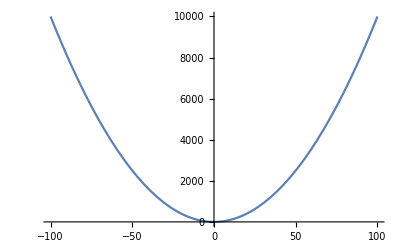
{-Graphics3D-,-Graphics-}

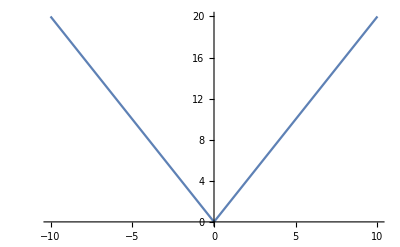
{-Graphics3D-,-Graphics-}

{-Graphics3D-,-Graphics-}

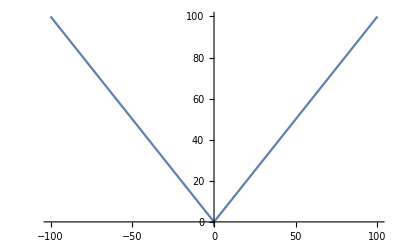
{-Graphics3D-,-Graphics-}

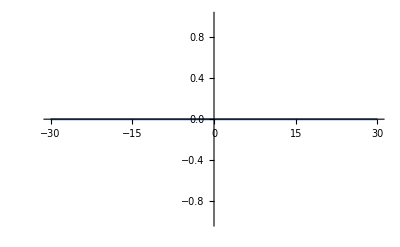
{-Graphics3D-,-Graphics-}

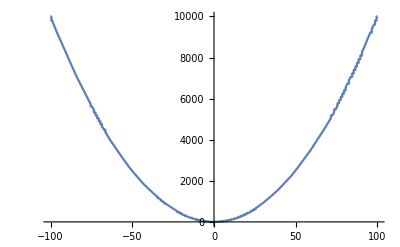
{-Graphics3D-,-Graphics-}

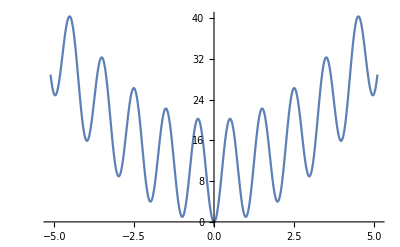
{-Graphics3D-,-Graphics-}

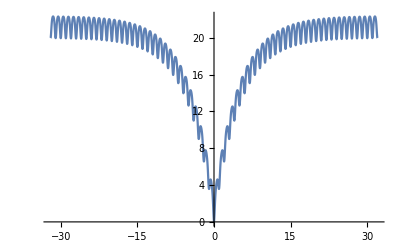
{-Graphics3D-,-Graphics-}

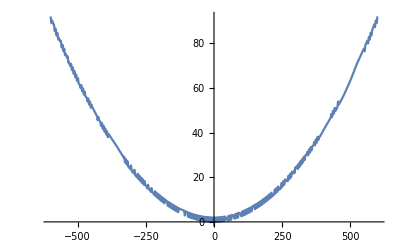
{-Graphics3D-,-Graphics-}

```mathematica
For[i=1,i<=9,i++,Print[{Plot3D[f[i][{x,y}],{x,-2,2},{y,-2,2}],Plot[f[i][{x}],{x,intervals[i][[1]], intervals[i][[2]]}]}]];
```

```mathematica
PRECITION=10;
ε=10^-PRECITION;
MAXITERATIONS=10000;
```

```mathematica
GSS[func_,a_,b_]:=Module[{ϕ=2./(3-√5),right=a,left=b,iteration=0,c,d},
c=right-(right-left)/ϕ;
d=left+(right-left)/ϕ;
While[Abs[right-left]>ε,
If[ func[{d}]>func[{c}],left=d,right=c];
	c=right-(right-left)/ϕ;
d=left+(right-left)/ϕ;
If[iteration==MAXITERATIONS,Print["Error",{N[left], N[right]}],iteration++;];
];
Return[(right+left)/2];
];
```

```mathematica
NewtonMethod[func_,x0_]:=Module[ {xCurr=x0,xPrev=x0-1,h=10.^-3},
While[Abs[xPrev-xCurr]>ε,
xPrev=xCurr;
xCurr=xPrev-h/2((func[{xPrev+h}]-func[{xPrev-h}])/(func[{xPrev+h}]-2func[{xPrev}]+func[{xPrev-h}]));
h=(10^-16 Abs[xCurr-xPrev])^(1/3);
(*xCurr=xPrev-h func'[xPrev];*)
];
Return[xCurr];
]
```

```mathematica
getAlpha[step_,Cp_]:=Cp/(1+step/2);
GradientDescent[func_,x0_,Cp_]:=Module[{h=10.^(-16/3),currentStep=0,currX=x0,α,gradient=Table[1,Length[x0]],hVec=Table[0,Length[x0]]},
While[Norm[gradient]>ε,
α=getAlpha[currentStep,Cp];

For[i=1,i<=Length[x0],i++,
hVec[[i]]=h;
gradient[[i]]=(func[currX+hVec]-func[currX-hVec])/(2h);
hVec[[i]]=0;
];
currX-=α gradient;
currentStep++;
If[currentStep==MAXITERATIONS,Return[currX]];
];
Return[currX];
]
```

```mathematica
PrintResult[method_,func_,args__]:=Module[{root},
root=method[func,args];
Print[func[Table[Subscript[x, i],{i,1,Length[{args}[[1]]]}]]," have root ",root, " and result of func equal ",func[root]];
]
```

```mathematica
For[j=1,j<=9,j++,
(*PrintResult[GSS, f[i],intervals[i][[1]], intervals[i][[2]]];*)
(*PrintResult[NewtonMethod, f[j],intervals[j][[1]]];*)
PrintResult[GradientDescent, f[j],{intervals[j][[1]],intervals[j][[1]]},Cp[j]];
]
```

x_1^2+x_2^2 have root {-1.96931×10^-11,-1.96931×10^-11} and result of func equal 7.75637×10^-22

Abs[x_1]+Abs[x_2]+Abs[x_1] Abs[x_2] have root {-0.00100085,-0.00100085} and result of func equal 0.0020027

x_1^2+(x_1+x_2)^2 have root {7.0442×10^-6,-0.0000113977} and result of func equal 6.85741×10^-11

Max[Abs[x_1],Abs[x_2]] have root {0.00802901,0.00802901} and result of func equal 0.00802901

(-1+x_1)^2+100 (-x_1^2+x_2)^2 have root {-3.70644×10^23,185970.} and result of func equal 1.88723×10^96

Floor[0.5+x_1]^2+Floor[0.5+x_2]^2 have root {-100.,-100.} and result of func equal 20000

20-10 Cos[2 π x_1]-10 Cos[2 π x_2]+x_1^2+x_2^2 have root {-2.61668×10^-13,-2.61668×10^-13} and result of func equal 0.

20+ⅇ-ⅇ^(1/2 (Cos[2 π x_1]+Cos[2 π x_2]))-20 ⅇ^(-0.141421 √(x_1^2+x_2^2)) have root {-30.9999,-30.9999} and result of func equal 19.9594

2-2 Cos[x_1] Cos[x_2/(√2)]+(x_1^2+x_2^2)/2000 have root {-599.702,-599.129} and result of func equal 359.617

```mathematica
getAlpha[step_,Cp_]:=Cp/(1+step/2);
GradientDescentEq[func_,x0_,Cp_]:=Module[{h=10.^(-16/3),currentStep=0,currX=x0,α,gradient=Table[1,Length[x0]]},
While[Norm[gradient]>ε,
α=getAlpha[currentStep,Cp];

gradient=Flatten[func[currX]];
currX-=α gradient;
currentStep++;
If[currentStep==MAXITERATIONS,Return[currX]];
];
Return[currX];
]
```

```mathematica
eq[x_]:={x}.A-b;
Chtoto[n_]:=Module[{},
dim = n;
A=Table[
Table[
If[i==j,2,1/Abs[i-j]]
,{j,1.,dim}
],{i, 1.,dim}
];
b={Table[{i^2},{i,1.,dim}]};
Return[GradientDescentEq[eq,Table[0,dim],1]];
];
Print[Chtoto[5]];
(*PrintResult[GradientDescentEq, eq,{0,0,0,0,0},1];*)
{-36861./26062,-6801./26062,369./332,52959./26062,297795./26062}
```

{-1.41436,-0.260952,1.11144,2.03204,11.4264}

{-1.41436,-0.260955,1.11145,2.03204,11.4264}

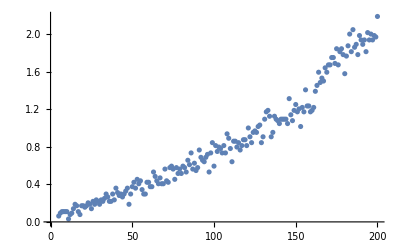

```mathematica
ListPlot[Table[{n,First[Timing[Chtoto[n]]]},{n,5,200}]]
```